STATISTIČNI PREGLED

1. UVOD
Glede na sezono 2018, sem si izbrala prvih 25 kobil z najboljšim rekordom.  Vsaki od kobil sem odčitala koliko štartov je imela v sezoni ter koliko štatrotv v karieri in  kolikokrat je bila uvrščena na 1., 2. oziroma tretje mesto.

v prvem grafu bom predstavila starost kobil ter število tekem v sezoni 2018. Naredila bom analizo starosti ( povprečna starost) ter povrepčeno število šatartov na konja.

```mathematica
Directory[]
```

C:\Users\Lapajne\Documents\faks\1.pra\rom\vajeposlano

```mathematica
NotebookDirectory[]
```

C:\Users\Lapajne\Documents\faks\1.pra\rom\seminarska naloga\

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Lapajne\Documents\faks\1.pra\rom\seminarska naloga

TABELA 1

```mathematica
tabela1 = TableForm[First[Import["tabela1.xlsx"]]]
```

ime konja | starost | število nastopov v 2018
ROMI MMS (IT) | 8. | 15.
PAOLENDRY LIKE (IT) | 9. | 13.
PETERKA I  | 4. | 15.
EROS JOSSELYN(FR) | 4. | 8.
DELUX MS | 6. | 3.
VILA AND GLORY (IT) | 4. | 13.
TARS STARS | 7. | 14.
DIDIER BLEU | 4. | 16.
ZAGABRIA VANI (IT) | 3. | 7.
ROADY DEL SILE(IT) | 8. | 15.
NARCIS PEŠKI | 7. | 11.
UNICA SPRIZT(IT) | 5. | 9.
ORIZZONTE TRIO (IT) | 10. | 6.
VIRGINIA BABA/IT) | 4. | 13.
SAMMI MS | 7. | 1.
THE WAY OF NANDO(IT) | 6. | 3.
VERA LIGHT(IT) | 4. | 9.
VITTORINA JET(IT) | 4. | 19.
BEAR GLIDE(SE) | 8. | 13.
ROŽLE | 6. | 12.
ISKRA KP | 4. | 10.
APOLLO | 9. | 6.
VANILLA MMS (IT) | 4. | 10.
PALMARIVATEKIHOVA (IT) | 9. | 10.
TAIGA GRIF (IT) | 6. | 10.

LEGENDA TABELE

```mathematica
Legenda[tabela1_] := First[First[tabela1]]
Legenda[tabela1]
```

{ime konja,starost,število nastopov v 2018}

VSI PODATKI TABELE

```mathematica
Podatki[tabela1_] := Rest[First[tabela1]]
Podatki[tabela1]
```

{{ROMI MMS (IT),8.,15.},{PAOLENDRY LIKE (IT),9.,13.},{PETERKA I ,4.,15.},{EROS JOSSELYN(FR),4.,8.},{DELUX MS,6.,3.},{VILA AND GLORY (IT),4.,13.},{TARS STARS,7.,14.},{DIDIER BLEU,4.,16.},{ZAGABRIA VANI (IT),3.,7.},{ROADY DEL SILE(IT),8.,15.},{NARCIS PEŠKI,7.,11.},{UNICA SPRIZT(IT),5.,9.},{ORIZZONTE TRIO (IT),10.,6.},{VIRGINIA BABA/IT),4.,13.},{SAMMI MS,7.,1.},{THE WAY OF NANDO(IT),6.,3.},{VERA LIGHT(IT),4.,9.},{VITTORINA JET(IT),4.,19.},{BEAR GLIDE(SE),8.,13.},{ROŽLE,6.,12.},{ISKRA KP,4.,10.},{APOLLO,9.,6.},{VANILLA MMS (IT),4.,10.},{PALMARIVATEKIHOVA (IT),9.,10.},{TAIGA GRIF (IT),6.,10.}}

INDEKS STOLPCA TABELE

```mathematica
IndeksStolpca[tabela1_,stolpec_] := Position[Legenda[tabela1], stolpec] //First // First
IndeksStolpca[tabela1, "število nastopov v 2018"]
```

3

PODATKI V DANEM STOLPCU

```mathematica
VrednostStolpca[tabela1_,stolpec_] := Transpose[Podatki[tabela1]][[IndeksStolpca[tabela1, stolpec]]]
VrednostStolpca[tabela1, "število nastopov v 2018"]
```

{15.,13.,15.,8.,3.,13.,14.,16.,7.,15.,11.,9.,6.,13.,1.,3.,9.,19.,13.,12.,10.,6.,10.,10.,10.}

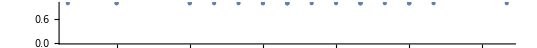

```mathematica
NumberLinePlot[{VrednostStolpca[tabela1, "število nastopov v 2018"]}]
```

POVPREČJE NASTOPOV

```mathematica
PovprecjeNastopov[tabela1_] := Mean[VrednostStolpca[tabela1, "število nastopov v 2018"]]
PovprecjeNastopov[tabela1]
```

10.44

STAROST KOBIL

```mathematica
VrednostStolpca[tabela1, "starost"]
```

{8.,9.,4.,4.,6.,4.,7.,4.,3.,8.,7.,5.,10.,4.,7.,6.,4.,4.,8.,6.,4.,9.,4.,9.,6.}

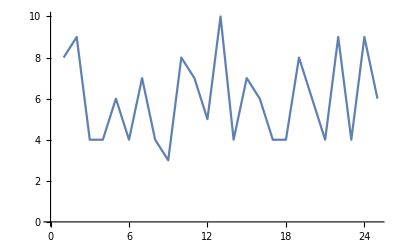

```mathematica
ListLinePlot[{VrednostStolpca[tabela1, "starost"]}]
```

POVPREČNA STAROST KOBIL

```mathematica
PovprecnaStarost[tabela1_] := Mean[VrednostStolpca[tabela1, "starost"]]
PovprecnaStarost[tabela1]
```

6.

STAROST NAJSTAREJŠE IN NAJMLAJŠE KOBILE

```mathematica
NajstarejsaKobila[tabela1_] = Max[VrednostStolpca[tabela1, "starost"]]
NajstarejsaKobila[tabela1]
```

10.

ime kobile:

```mathematica
NajmlajsaKobila[tabela1_] := Min[VrednostStolpca[tabela1, "starost"]]
NajmlajsaKobila[tabela1]
```

3.

ime kobile:

v drugi tabeli so podatki števila štartov v sezoni 2018 ter kolikokrat je dana kobila dosegla prvo, drugo ali tretje mesto. Izračunala bom povprečje štartov, uvrstitev prvega, drugega in tretjega mesta. Minimum ter maksimum vsake vrednosti.

```mathematica
NotebookDirectory[]
```

C:\Users\Lapajne\Documents\faks\1.pra\rom\seminarska naloga\

```mathematica
tabela2 = TableForm[First[Import["tabela2.xlsx"]]]
```

ime konja/mesto | št. štartov | uvrstitev na 1. mesto | uvrstitev na 2. mesto | uvrstitev na 3. mesto
ROMI MMS (IT) | 74. | 26. | 7. | 10.
PAOLENDRY LIKE (IT) | 23. | 3. | 6. | 3.
PETERKA I  | 31. | 10. | 2. | 3.
EROS JOSSELYN(FR) | 9. | 7. | 1. | 0.
DELUX MS | 28. | 16. | 1. | 1.
VILA AND GLORY (IT) | 26. | 7. | 3. | 6.
TARS STARS | 65. | 17. | 19. | 11.
DIDIER BLEU | 30. | 13. | 9. | 5.
ZAGABRIA VANI (IT) | 11. | 2. | 5. | 0.
ROADY DEL SILE(IT) | 89. | 16. | 18. | 9.
NARCIS PEŠKI | 51. | 21. | 8. | 7.
UNICA SPRIZT(IT) | 11. | 0. | 1. | 0.
ORIZZONTE TRIO (IT) | 20. | 5. | 0. | 4.
VIRGINIA BABA/IT) | 28. | 4. | 7. | 5.
SAMMI MS | 48. | 21. | 8. | 4.
THE WAY OF NANDO(IT) | 26. | 8. | 4. | 1.
VERA LIGHT(IT) | 9. | 0. | 2. | 0.
VITTORINA JET(IT) | 29. | 9. | 7. | 3.
BEAR GLIDE(SE) | 55. | 10. | 10. | 7.
ROŽLE | 43. | 13. | 4. | 7.
ISKRA KP | 22. | 4. | 4. | 3.
APOLLO | 83. | 12. | 14. | 9.
VANILLA MMS (IT) | 23. | 7. | 5. | 1.
PALMARIVATEKIHOVA (IT) | 12. | 1. | 3. | 3.
TAIGA GRIF (IT) | 41. | 4. | 6. | 5.

```mathematica
Legenda[tabela2]
```

{ime konja/mesto,št. štartov,1.,2.,3.}

ŠTEVILO ŠTARTOV

```mathematica
VrednostStolpca[tabela2, "št. štartov"]
```

First::nofirst: {} has zero length and no first element.

{}

POVPREČNO ŠTEVILO NASTOPOV

```mathematica
PovprecjeNastopov[
```

NAJVEČJE IN NAJMANJŠE ŠTEVILO NASTOPOV

POVPREČNA UVRSTITEV NA 1. MESTO

POVPREČNA UVRSTITEV NA 2. MESTO

POVPREČNA UVRSTITEV NA 3. MESTO